## Deriving Equations of Motion for Scalar Perturbation

The metric is given by ds^2=-(1-Mc/r)dt^2+(1-Ms/r)dy^2+dr^2/((1-Mc/r)(1-Ms/r))+r^2(dθ^2+Sin^2[θ]dϕ^2)

The Ricci Tensor with μ=(t,r,θ,ϕ,y) is given by R_μν=Diag[(Mc Ms(1-Mc/r))/(2 r^4),-(Mc Ms)/(2r^4(1-Mc/r)(1-Ms/r)),(Mc Ms)/r^2,(Mc Ms Sin^2[θ])/r^2,-(Mc Ms (1-Ms/r))/(2 r^4)]

We want to first describe a scalar perturbation in this geometry, and see what kind of behavior we get. This can lead to initial studies of QNM’s. We can later compare and contrast against the standard Schwarzschild observables

The standard wave equation for a scalar is given by □Φ=1/(√-det g)∂_μ ((√-det g)g^μν∂_ν Φ)=m^2 Φ

```mathematica
Exit[]
```

```mathematica
coords = {t,r,θ,ϕ,y};
```

define g_μν

```mathematica
gμν=DiagonalMatrix[{-(1-Mc/r),(1-Mc/r)^-1(1-Ms/r)^-1,r^2,r^2(Sin[θ])^2,(1-Ms/r)}];
```

```mathematica
gμν//MatrixForm
```

(-1+Mc/r | 0 | 0 | 0 | 0
0 | 1/((1-Mc/r) (1-Ms/r)) | 0 | 0 | 0
0 | 0 | r^2 | 0 | 0
0 | 0 | 0 | r^2 Sin[θ]^2 | 0
0 | 0 | 0 | 0 | 1-Ms/r)

Define g^μν

```mathematica
Invgμν=Inverse[gμν]//Simplify;
```

```mathematica
Invgμν//MatrixForm
```

(r/(Mc-r) | 0 | 0 | 0 | 0
0 | ((Mc-r) (Ms-r))/r^2 | 0 | 0 | 0
0 | 0 | 1/r^2 | 0 | 0
0 | 0 | 0 | Csc[θ]^2/r^2 | 0
0 | 0 | 0 | 0 | -r/(Ms-r))

```mathematica
g=Det[gμν]//Simplify
```

-r^4 Sin[θ]^2

Plug in these quantities to 1/(√-det g)∂_μ ((√-det g)g^μν∂_ν Φ)-m^2 Φ=0 to find the EoM for Φ in this metric

```mathematica
Eq1=Sum[1/Sqrt[-g] D[Sqrt[-g]Invgμν[[μ,ν]]*D[Φ[t,r,θ,ϕ,y],coords[[ν]]],coords[[μ]]],{μ,1,5},{ν,1,5}]+m^2 Φ[t,r,θ,ϕ,y]//Simplify
```

1/((Ms-r) r^2 (-Mc+r))(m^2 (Mc-r) r^2 (-Ms+r) Φ[t,r,θ,ϕ,y]+(Mc-r) r^3 Φ^(0,0,0,0,2)[t,r,θ,ϕ,y]-(Ms-r) ((Mc-r) Csc[θ]^2 Φ^(0,0,0,2,0)[t,r,θ,ϕ,y]+(Mc-r) Cot[θ] Φ^(0,0,1,0,0)[t,r,θ,ϕ,y]+Mc Φ^(0,0,2,0,0)[t,r,θ,ϕ,y]-r Φ^(0,0,2,0,0)[t,r,θ,ϕ,y]-Mc^2 Φ^(0,1,0,0,0)[t,r,θ,ϕ,y]-Mc Ms Φ^(0,1,0,0,0)[t,r,θ,ϕ,y]+3 Mc r Φ^(0,1,0,0,0)[t,r,θ,ϕ,y]+Ms r Φ^(0,1,0,0,0)[t,r,θ,ϕ,y]-2 r^2 Φ^(0,1,0,0,0)[t,r,θ,ϕ,y]+Mc^2 Ms Φ^(0,2,0,0,0)[t,r,θ,ϕ,y]-Mc^2 r Φ^(0,2,0,0,0)[t,r,θ,ϕ,y]-2 Mc Ms r Φ^(0,2,0,0,0)[t,r,θ,ϕ,y]+2 Mc r^2 Φ^(0,2,0,0,0)[t,r,θ,ϕ,y]+Ms r^2 Φ^(0,2,0,0,0)[t,r,θ,ϕ,y]-r^3 Φ^(0,2,0,0,0)[t,r,θ,ϕ,y]+r^3 Φ^(2,0,0,0,0)[t,r,θ,ϕ,y]))

We can expand in Fourier modes along the isometries (the metric is free of ϕ, y, and t, so Φ ∝ e^(ⅈ(ω t + k y + n ϕ )))

```mathematica
Eq2=Sum[1/Sqrt[-g] D[Sqrt[-g]Invgμν[[μ,ν]]*D[T[t]*R[r]/f[r]*Θ[θ]*W[ϕ]*Q[y],coords[[ν]]],coords[[μ]]],{μ,1,5},{ν,1,5}]+m^2*T[t]*R[r]/f[r]*Θ[θ]*W[ϕ]*Q[y]//Simplify
```

1/f[r]^3(m^2 f[r]^2 Q[y] R[r] T[t] W[ϕ] Θ[θ]+((Mc-r) f[r] Q[y] T[t] W[ϕ] Θ[θ] (R[r] f'[r]-f[r] R'[r]))/r^2+((Ms-r) f[r] Q[y] T[t] W[ϕ] Θ[θ] (R[r] f'[r]-f[r] R'[r]))/r^2-(r f[r]^2 R[r] T[t] W[ϕ] Θ[θ] Q''[y])/(Ms-r)-((Mc-r) (-Ms+r) Q[y] T[t] W[ϕ] Θ[θ] (R[r] (2 f'[r]^2-f[r] f''[r])+f[r] (-2 f'[r] R'[r]+f[r] R''[r])))/r^2+(r f[r]^2 Q[y] R[r] W[ϕ] Θ[θ] T''[t])/(Mc-r)+(Csc[θ]^2 f[r]^2 Q[y] R[r] T[t] Θ[θ] W''[ϕ])/r^2+(f[r]^2 Q[y] R[r] T[t] W[ϕ] (Cot[θ] Θ'[θ]+Θ''[θ]))/r^2)

Divide out Φ

```mathematica
Eq3=f[r]^3*Eq2/(T[t]*R[r]*Θ[θ]*W[ϕ]*Q[y])//Simplify
```

(2 (Mc-r) (Ms-r) f'[r]^2)/r^2+(f[r] (2 (Mc-r) (-Ms+r) f'[r] R'[r]+R[r] ((Mc+Ms-2 r) f'[r]+(Mc-r) (-Ms+r) f''[r])))/(r^2 R[r])+f[r]^2 (m^2-(r Q''[y])/((Ms-r) Q[y])+(-(Mc+Ms-2 r) R'[r]+(Mc-r) (Ms-r) R''[r])/(r^2 R[r])+(r T''[t])/((Mc-r) T[t])+(Csc[θ]^2 W''[ϕ])/(r^2 W[ϕ])+(Cot[θ] Θ'[θ]+Θ''[θ])/(r^2 Θ[θ]))

Multiply by (Ms-r)/r to isolate Q[y]

```mathematica
Eq4=1/Coefficient[Eq3,Q''[y]/Q[y]]*Eq3//Distribute//FullSimplify
```

1/r^3(m^2 r^2 (-Ms+r)-(2 (Mc-r) (Ms-r)^2 f'[r]^2)/f[r]^2+((-Ms+r) Cot[θ] Θ'[θ])/Θ[θ]+((Ms-r) (f'[r] (-(Mc+Ms-2 r) R[r]+2 (Mc-r) (Ms-r) R'[r])+(Mc-r) (Ms-r) R[r] f''[r]))/(f[r] R[r])+(r^3 Q''[y])/Q[y]+((Ms-r) ((Mc+Ms-2 r) R'[r]+(Mc-r) (-Ms+r) R''[r]))/R[r]+(r^3 (-Ms+r) T''[t])/((Mc-r) T[t])+((-Ms+r) Csc[θ]^2 W''[ϕ])/W[ϕ]+((-Ms+r) Θ''[θ])/Θ[θ])

We have a portion Q’’[y]/Q[y] only dependent on y, and the rest depends on the other variables. This allows us to set the Q term equal to -k^2, and set the rest to +k^2. This means that Q[y] = e^ⅈky. Note that k is limited to particular values by the condition that y parameterizes a circle with period 2π R_y. Can write y=ϕ_y R_y, and ϕ_y is 2π periodic. Because of this periodicity, e^(ikϕ_y R_y)=e^(ik(ϕ_y+2π)R_y), so e^ik2πR_y=1. This only happens for Cos[2π k R_y] = 1, implying that 2π k R_y = n*2π , implying that k = n/R_y, where n ∈ ℤ.

```mathematica
Eq5 = Eq4/.Q[y]->ⅇ^(ⅈ k y)/.Q''[y]->-k^2 ⅇ^(ⅈ k y)//Distribute
```

-k^2+(m^2 (-Ms+r))/r-(2 (Mc-r) (Ms-r)^2 f'[r]^2)/(r^3 f[r]^2)+((-Ms+r) Cot[θ] Θ'[θ])/(r^3 Θ[θ])+((Ms-r) (f'[r] (-(Mc+Ms-2 r) R[r]+2 (Mc-r) (Ms-r) R'[r])+(Mc-r) (Ms-r) R[r] f''[r]))/(r^3 f[r] R[r])+((Ms-r) ((Mc+Ms-2 r) R'[r]+(Mc-r) (-Ms+r) R''[r]))/(r^3 R[r])+((-Ms+r) T''[t])/((Mc-r) T[t])+((-Ms+r) Csc[θ]^2 W''[ϕ])/(r^3 W[ϕ])+((-Ms+r) Θ''[θ])/(r^3 Θ[θ])

Now multiply everything by (Mc-r)/(-Ms+r) to isolate t

```mathematica
Eq6 = (Mc-r)/(-Ms+r)Eq5//Distribute//FullSimplify
```

1/r^3(((Mc-r) r^2 (m^2 (Ms-r)+k^2 r))/(Ms-r)+(2 (Mc-r)^2 (Ms-r) f'[r]^2)/f[r]^2+((Mc-r) (f'[r] ((Mc+Ms-2 r) R[r]+2 (Mc-r) (-Ms+r) R'[r])+(Mc-r) (-Ms+r) R[r] f''[r]))/(f[r] R[r])+((-Mc+r) ((Mc+Ms-2 r) R'[r]+(Mc-r) (-Ms+r) R''[r]))/R[r]+(r^3 T''[t])/T[t]+((Mc-r) Csc[θ]^2 W''[ϕ])/W[ϕ]+((Mc-r) (Cot[θ] Θ'[θ]+Θ''[θ]))/Θ[θ])

Since the terms with T’’[t]/T[t] only depend on t, and the rest depend on the other variables, we can again set T’’[t]/T[t] = -ω^2, and set the rest to +ω^2. This means that T[t] = e^(ⅈ ω t).

```mathematica
Eq7 = Eq6/.T[t]->ⅇ^(ⅈ ω t)/.T''[t]->-ω^2 ⅇ^(ⅈ ω t)//Distribute//FullSimplify
```

m^2 (-1+Mc/r)+(k^2 (Mc-r))/(Ms-r)-ω^2+1/(r^3 f[r]^2 R[r] W[ϕ] Θ[θ])(Mc-r) (2 (Mc-r) (Ms-r) R[r] W[ϕ] Θ[θ] f'[r]^2+f[r] W[ϕ] Θ[θ] (f'[r] ((Mc+Ms-2 r) R[r]+2 (Mc-r) (-Ms+r) R'[r])+(Mc-r) (-Ms+r) R[r] f''[r])+f[r]^2 (Csc[θ]^2 R[r] Θ[θ] W''[ϕ]+W[ϕ] (Θ[θ] (-(Mc+Ms-2 r) R'[r]+(Mc-r) (Ms-r) R''[r])+R[r] (Cot[θ] Θ'[θ]+Θ''[θ]))))

Multiply by r^3/((Mc-r) Csc[θ]^2)to isolate the ϕ terms

```mathematica
Eq8=r^3/(Mc-r)(1/Csc[θ])^2 Eq7//Distribute//FullSimplify
```

Sin[θ]^2 (r^2 (m^2+(k^2 r)/(Ms-r)+(r ω^2)/(-Mc+r))+(2 (Mc-r) (Ms-r) f'[r]^2)/f[r]^2+(f'[r] ((Mc+Ms-2 r) R[r]+2 (Mc-r) (-Ms+r) R'[r])+(Mc-r) (-Ms+r) R[r] f''[r])/(f[r] R[r])+(-(Mc+Ms-2 r) R'[r]+(Mc-r) (Ms-r) R''[r])/R[r]+(Csc[θ]^2 W''[ϕ])/W[ϕ]+(Cot[θ] Θ'[θ]+Θ''[θ])/Θ[θ])

Again, we notice that the W’’[ϕ]/W[ϕ] term is the only one containing ϕ. We can set this term to -q^2 (usually use -m^2, but use q to avoid confusion with the scalar field’s mass) and set the rest to +q^2. This means that W[ϕ] = e^(i q ϕ).)

```mathematica
Eq9 = Eq8/.W[ϕ]->ⅇ^(ⅈ q ϕ)/.W''[ϕ]->-q^2 ⅇ^(ⅈ q ϕ)//Distribute//FullSimplify
```

-q^2+r^2 (m^2+(k^2 r)/(Ms-r)+(r ω^2)/(-Mc+r)) Sin[θ]^2+(2 (Mc-r) (Ms-r) Sin[θ]^2 f'[r]^2)/f[r]^2+(Sin[θ]^2 (f'[r] ((Mc+Ms-2 r) R[r]+2 (Mc-r) (-Ms+r) R'[r])+(Mc-r) (-Ms+r) R[r] f''[r]))/(f[r] R[r])+(Sin[θ]^2 (-(Mc+Ms-2 r) R'[r]+(Mc-r) (Ms-r) R''[r]))/R[r]+(Sin[θ]^2 (Cot[θ] Θ'[θ]+Θ''[θ]))/Θ[θ]

Can separate further, by multiplying this new equation by 1/Sin[θ]^2

```mathematica
Eq10 = Collect[((1/Sin[θ])^2 Eq9//FullSimplify),{R''[r],R'[r],R[r]}]
```

r^2 (m^2+(k^2 r)/(Ms-r)+(r ω^2)/(-Mc+r))-q^2 Csc[θ]^2+((Mc+Ms-2 r) f'[r])/f[r]+(2 (Mc-r) (Ms-r) f'[r]^2)/f[r]^2+((-Mc-Ms+2 r+(2 (Mc-r) (-Ms+r) f'[r])/f[r]) R'[r])/R[r]+((Mc-r) (-Ms+r) f''[r])/f[r]+((Mc-r) (Ms-r) R''[r])/R[r]+(Cot[θ] Θ'[θ]+Θ''[θ])/Θ[θ]

We see that we have a portion which only depends on θ, and a portion which only depends on r. Set the θ portion equal to -λ, and set the r portion equal to λ. Multiply the r equation by R[r], and the θ equation by Θ[θ]

```mathematica
rEq = R[r](r^2 (m^2+(k^2 r)/(Ms-r)+(r ω^2)/(-Mc+r))+((Mc+Ms-2 r) f'[r])/f[r]+(2 (Mc-r) (Ms-r) f'[r]^2)/f[r]^2+((-Mc-Ms+2 r+(2 (Mc-r) (-Ms+r) f'[r])/f[r]) R'[r])/R[r]+((Mc-r) (-Ms+r) f''[r])/f[r]+((Mc-r) (Ms-r) R''[r])/R[r]-λ)//Simplify
```

-λ R[r]+r^2 (m^2+(k^2 r)/(Ms-r)+(r ω^2)/(-Mc+r)) R[r]+((Mc+Ms-2 r) R[r] f'[r])/f[r]+(2 (Mc-r) (Ms-r) R[r] f'[r]^2)/f[r]^2+(-Mc-Ms+2 r+(2 (Mc-r) (-Ms+r) f'[r])/f[r]) R'[r]+((Mc-r) (-Ms+r) R[r] f''[r])/f[r]+(Mc-r) (Ms-r) R''[r]

```mathematica
θEq=Θ[θ]((Cot[θ] Θ'[θ]+Θ''[θ])/Θ[θ]-q^2 Csc[θ]^2+λ)//Simplify
```

(λ-q^2 Csc[θ]^2) Θ[θ]+Cot[θ] Θ'[θ]+Θ''[θ]

The θ equation is just the regular spherical harmonic equation, with solutions given by the Legendre Functions. q serves as the usual “magnetic quantum number”, and we should set λ=l(l+1) as usual for the spherical harmonic equations.

Note: Pierre sets λ = l(l+2), and I’m not sure why he uses l+2 instead of l+1

Setting λ=l(l+1), we can rewrite the R[r] equation in order to find an equation for radial waves analogous to the Schwarzschild radial wave equation.

```mathematica
rEq1=rEq/.λ->l(l+1)
```

-l (1+l) R[r]+r^2 (m^2+(k^2 r)/(Ms-r)+(r ω^2)/(-Mc+r)) R[r]+((Mc+Ms-2 r) R[r] f'[r])/f[r]+(2 (Mc-r) (Ms-r) R[r] f'[r]^2)/f[r]^2+(-Mc-Ms+2 r+(2 (Mc-r) (-Ms+r) f'[r])/f[r]) R'[r]+((Mc-r) (-Ms+r) R[r] f''[r])/f[r]+(Mc-r) (Ms-r) R''[r]

```mathematica
(*********************************************************************************************)
```

The usual prescription is to change to Tortoise coordinates, defined typically by  dr_*/dr=(1-Mc/r)^-1. Here, we instead choose dr_*/dr general enough to later prescribe something:

```mathematica
rEq2=Collect[rEq1/.R'[r]-> D[rs[r],r]*R'[r]/.R''[r]->( D[rs[r],r,r]*R'[r]+(D[rs[r],r])^2 R''[r])/.R[r]->R[r],{R[r],R'[r],R''[r]},FullSimplify]
```

R[r] (-l (1+l)+r^2 (m^2+(k^2 r)/(Ms-r)+(r ω^2)/(-Mc+r))+(2 (Mc-r) (Ms-r) f'[r]^2+f[r] ((Mc+Ms-2 r) f'[r]+(Mc-r) (-Ms+r) f''[r]))/f[r]^2)+(Mc-r) (Ms-r) rs'[r]^2 R''[r]+R'[r] ((-Mc-Ms+2 r+(2 (Mc-r) (-Ms+r) f'[r])/f[r]) rs'[r]+(Mc-r) (Ms-r) rs''[r])

The primes now denote derivates wrt r_*when on R[rs], and w.r.t. r when on the rs[r] functions. Now we want to get rid of the R’[r] term by making an appropriate choice of rs:

```mathematica
DSolve[((-Mc-Ms+2 r+(2 (Mc-r) (-Ms+r) f'[r])/f[r]) rs'[r]+(Mc-r) (Ms-r) rs''[r])==0,rs[r],r]
```

{{rs[r]→C[2]+(C[1] f[K[1]]^2)/((-Mc+K[1]) (-Ms+K[1]))K[1]1r}}

```mathematica
Integrate[(w-Mc)/(-Ms+w),w]/.w->r
```

r+(-Mc+Ms) Log[-Ms+r]

```mathematica
rEq3=Collect[ (Ms-r)/(Mc-r)^5*f[r]^2*rEq2/.rs->Function[r,r+(-Mc+Ms) Log[-Ms+r]]/.f->Function[r,r-Mc]/.R[r]->R[rs]/.R''[r]->R''[rs],{R[rs],R''[rs]},FullSimplify]
```

((Ms-r) (-l (1+l)+r^2 (m^2+(k^2 r)/(Ms-r))-(Mc-Ms+r^3 ω^2)/(Mc-r)) R[rs])/(Mc-r)^3+R''[rs]

```mathematica
Veff=-Coefficient[rEq3,R[rs]]
```

-((Ms-r) (-l (1+l)+r^2 (m^2+(k^2 r)/(Ms-r))-(Mc-Ms+r^3 ω^2)/(Mc-r)))/(Mc-r)^3

This is the Schrodinger-Like equation that we typically expect from the Schwarzschild solution of this problem, with the effective potential Veff[r].

With the choice f[r] = r:

```mathematica
Veff=-((Mc-r) (Ms-r) (-l (1+l)+(2 Mc Ms-(Mc+Ms) r)/r^2+r^2 (m^2+(k^2 r)/(Ms-r)+(r ω^2)/(-Mc+r))))/r^4
```

Check that we recover the Schwarzschild regge-wheeler eqn.

```mathematica
VRW=-ω^2+(1-Mc/r)((l(l+1))/r^2+Mc/r^3)
```

(Mc/r^3+(l (1+l))/r^2) (1-Mc/r)-ω^2

```mathematica
(Veff/.Ms->0/.m->0/.k->0)-VRW//FullSimplify
```

0

With a different choice for the function f[r] (f[r] = r-rs)

```mathematica
Veff=(r-Ms)/(r-Mc)^3 ((k^2 r^3)/(r-Ms)-(ω^2 r^3)/(r-Mc)+l (1+l)+(Ms-Mc)/(r-Mc)-m^2 r^2);
```

Turning points?

```mathematica
NSolve[((r-Ms)/(r-Mc)^3 ((k^2 r^3)/(r-Ms)-(ω^2 r^3)/(r-Mc)+l (1+l)+(Ms-Mc)/(r-Mc)-m^2 r^2)==0/.k->0/.m->0/.l->1/.Mc->29/.Ms->31/.ω->1/80),r]//Simplify
```

{{r→-125.155},{r→95.0158},{r→31.},{r→30.1388}}

Highly dependent on the parameter choices!

```mathematica
(*********************************************************************************************)
```

```mathematica
(*********************************************************************************************)
```

```mathematica
(*********************************************************************************************)
```

```mathematica
(*********************************************************************************************)
```

What is below comes from a different choice of the rst coordinate, and a different choice for the function f[r]

### other coordinate choice

Next, we can use the effective potential to investigate how modes propagate. A possible method of attack is the WKB approximation. To use this or some other approximation scheme, it’s helpful to know the boundary conditions of the effective potential in the various cases. There should be some region where the potential is negative, followed by some positive potential barrier, then followed by some negative tail as r goes to infinity if we are to expect to see QNM’s. These features must exist outside of r = Mc or r = Ms, depending on which is bigger. If Mc > Ms, Ms is the “end” to spacetime. The opposite is true if Ms > Mc.

Taking Ms->0 (Also Ry->0, so k-> 0) gives back the standard Schwarzschild Veff[r]

We should examine two cases, the Mc > Ms case, and the Ms > Mc case.

```mathematica
Veff=-1/r^6(Mc^2 (2 Ms^2-3 Ms r+r^2)+Mc r (-3 Ms^2-Ms r (-4+l+l^2+m^2 r^2)+r^2 (-1+l+l^2+k^2 r^2+m^2 r^2))+r^2 (Ms^2+Ms r (-1+l+l^2+m^2 r^2-r^2 ω^2)-r^2 (l+l^2+r^2 (k^2+m^2-ω^2))))
```

```mathematica
(1-Mc/r) (1-Ms/r) (k^2/(1-Ms/r)+(l (1+l))/r^2+(-2 Mc Ms+(Mc+Ms) r+m^2 r^4)/r^4-ω^2/(1-Mc/r))
```

0

```mathematica
Series[Veff,{r,Ms,0}]//FullSimplify
```

(k^2 Ms^3)/(-Mc+Ms)^3+O[r-Ms]^1

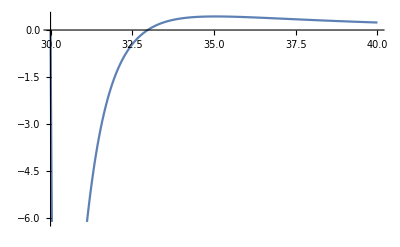

```mathematica
Plot[{Veff/.Mc->29/.l->9/.Ms->30/.k->0/.ω->0.1/.m->0},{r,30,40},PlotRange->{All,Automatic}]
```

There are some choices of the parameters which result in the appropriate potential behavior for QNM’s in the Ms > Mc case

Let’s examine some of the conditions for when QNM’s can appear. We need at least 2 turning points. We need some negative potential well, followed by a positive potential barrier, and need the potential to drop back to negative as r-> infinity. We can examine some of these conditions by considering the large r behavior, and maybe trying to find some solution for Veff(r) = 0.

```mathematica
Series[Veff,{r,∞,0}]
```

(k^2+m^2-ω^2)+O[1/r]^1

For r→ ∞ , in the Ms > Mc case, the behavior of the potential is governed by k^2+m^2-ω^2. We need this quantity to be negative to have Veff[r→ ∞]<0.

```mathematica
NSolve[Veff==0/.Mc->1.3/.l->0/.Ms->1.4/.k->0/.ω->1/10/.m->0,r,Reals]
```

{{r→1.22097},{r→1.4},{r→1.49103},{r→5.34638}}

```mathematica
Series[Veff,{r,Mc,0}]
```

(-Mc ω^2+Ms ω^2)/Mc+O[r-Mc]^1

For Ms > Mc case, near r = Mc we will have some positive Veff since -(1-Ms/Mc) ω^2 will be positive.

```mathematica
Series[Veff,{r,Ms,0}]
```

(-k^2 Mc+k^2 Ms)/Ms+O[r-Ms]^1

For Mc > Ms case, near r = Ms we will always have some negative Veff since k^2(1-Mc/Ms) will be negative in this case.

```mathematica
Solve[Normal[Series[Veff,{r,Mc,1}]]==0,r]//FullSimplify
```

{{r→(Mc ((1+l+l^2) Mc^2+m^2 Mc^5-(2+l+l^2) Mc Ms+Ms^2-2 Mc^3 Ms ω^2+Mc^4 (k^2-m^2 Ms+ω^2)))/((1+l+l^2) Mc^2+m^2 Mc^5-(2+l+l^2) Mc Ms+Ms^2+Mc^4 (k^2-m^2 Ms)-Mc^3 Ms ω^2)}}

```mathematica
D[Veff,r]//FullSimplify
```

1/r^7(Mc^2 (12 Ms^2-15 Ms r+4 r^2)+Mc r (-15 Ms^2-4 (-4+l+l^2) Ms r+3 (-1+l+l^2) r^2+(k^2-m^2 Ms) r^4)+r^2 (4 Ms^2+3 (-1+l+l^2) Ms r-2 l (1+l) r^2+m^2 r^5-Ms r^3 ω^2))

```mathematica
Solve[Veff==0/.m->0/.l->0/.k->0,r]
```

{{r→Ms},{r→Root[-2 Mc^2 Ms+(Mc^2+3 Mc Ms) #1+(-Mc-Ms) #1^2+ω^2 #1^5&,1]},{r→Root[-2 Mc^2 Ms+(Mc^2+3 Mc Ms) #1+(-Mc-Ms) #1^2+ω^2 #1^5&,2]},{r→Root[-2 Mc^2 Ms+(Mc^2+3 Mc Ms) #1+(-Mc-Ms) #1^2+ω^2 #1^5&,3]},{r→Root[-2 Mc^2 Ms+(Mc^2+3 Mc Ms) #1+(-Mc-Ms) #1^2+ω^2 #1^5&,4]},{r→Root[-2 Mc^2 Ms+(Mc^2+3 Mc Ms) #1+(-Mc-Ms) #1^2+ω^2 #1^5&,5]}}

```mathematica
Solve[D[Veff,r]==0/.m->0/.l->0/.k->0,r]
```

{{r→Root[-12 Mc^2 Ms^2+(15 Mc^2 Ms+15 Mc Ms^2) #1+(-4 Mc^2-16 Mc Ms-4 Ms^2) #1^2+(3 Mc+3 Ms) #1^3+Ms ω^2 #1^5&,1]},{r→Root[-12 Mc^2 Ms^2+(15 Mc^2 Ms+15 Mc Ms^2) #1+(-4 Mc^2-16 Mc Ms-4 Ms^2) #1^2+(3 Mc+3 Ms) #1^3+Ms ω^2 #1^5&,2]},{r→Root[-12 Mc^2 Ms^2+(15 Mc^2 Ms+15 Mc Ms^2) #1+(-4 Mc^2-16 Mc Ms-4 Ms^2) #1^2+(3 Mc+3 Ms) #1^3+Ms ω^2 #1^5&,3]},{r→Root[-12 Mc^2 Ms^2+(15 Mc^2 Ms+15 Mc Ms^2) #1+(-4 Mc^2-16 Mc Ms-4 Ms^2) #1^2+(3 Mc+3 Ms) #1^3+Ms ω^2 #1^5&,4]},{r→Root[-12 Mc^2 Ms^2+(15 Mc^2 Ms+15 Mc Ms^2) #1+(-4 Mc^2-16 Mc Ms-4 Ms^2) #1^2+(3 Mc+3 Ms) #1^3+Ms ω^2 #1^5&,5]}}

```mathematica
D[Veff,r]/.m->0/.l->0/.k->0//Simplify
```

(Mc r (-15 Ms^2+16 Ms r-3 r^2)+Mc^2 (12 Ms^2-15 Ms r+4 r^2)+Ms r^2 (4 Ms-r (3+r^2 ω^2)))/r^7

```mathematica
(*********************************************************************************************)
```

Let’s rewrite some things in terms of the ADM mass and charge

```mathematica
Solve[{ℳ==2π(2Mc+Ms)/κ^2,𝒬^2==3/2(Ms Mc)/κ^2},{Ms,Mc}]//Simplify
```

{{Ms→-(-3 ℳ κ^2+√(-192 π^2 𝒬^2 κ^2+9 ℳ^2 κ^4))/(12 π),Mc→(3 ℳ κ^2+√(-192 π^2 𝒬^2 κ^2+9 ℳ^2 κ^4))/(24 π)},{Ms→(3 ℳ κ^2+√(-192 π^2 𝒬^2 κ^2+9 ℳ^2 κ^4))/(12 π),Mc→-(-3 ℳ κ^2+√(-192 π^2 𝒬^2 κ^2+9 ℳ^2 κ^4))/(24 π)}}

```mathematica
Veff/.Ms-> -(-3 ℳ κ^2+√(-192 π^2 𝒬^2 κ^2+9 ℳ^2 κ^4))/(12 π)/.Mc-> (3 ℳ κ^2+√(-192 π^2 𝒬^2 κ^2+9 ℳ^2 κ^4))/(24 π)//Simplify
```

-1/r^6(1/(24 π)r (3 ℳ κ^2+√(-192 π^2 𝒬^2 κ^2+9 ℳ^2 κ^4)) (r^2 (-1+l+l^2+k^2 r^2+m^2 r^3)+(r (-4+l+l^2+m^2 r^3) (-3 ℳ κ^2+√(-192 π^2 𝒬^2 κ^2+9 ℳ^2 κ^4)))/(12 π)-((-3 ℳ κ^2+√(-192 π^2 𝒬^2 κ^2+9 ℳ^2 κ^4))^2)/(48 π^2))+(κ^2 (-32 π^2 (3 r^2 𝒬^2-8 𝒬^4 κ^2)+3 r^2 ℳ (3 ℳ κ^2+√(-192 π^2 𝒬^2 κ^2+9 ℳ^2 κ^4))-24 π r 𝒬^2 (3 ℳ κ^2+√(-192 π^2 𝒬^2 κ^2+9 ℳ^2 κ^4))))/(288 π^2)+r^2 (((-3 ℳ κ^2+√(-192 π^2 𝒬^2 κ^2+9 ℳ^2 κ^4))^2)/(144 π^2)-(r (-3 ℳ κ^2+√(-192 π^2 𝒬^2 κ^2+9 ℳ^2 κ^4)) (-1+l+l^2+m^2 r^3-r^2 ω^2))/(12 π)-r^2 (l+l^2+r^2 (k^2+m^2 r-ω^2))))

Let’s examine when Ms is > Mc and vice versa for the different solutions

Limited by 𝒬^2/κ^2≤3/64 ℳ^2

Have  Ms=ℳ κ^2/(4π)(1±Sqrt[1-64/3 π^2/κ^2 𝒬^2/ℳ^2]) and Mc=ℳ κ^2/(8π)(1∓Sqrt[1-64/3 π^2/κ^2 𝒬^2/ℳ^2])

```mathematica
(ℳ κ^2 (1±√(1-(64 π^2 𝒬^2)/(3 κ^2 ℳ^2))))/(4 π)
```

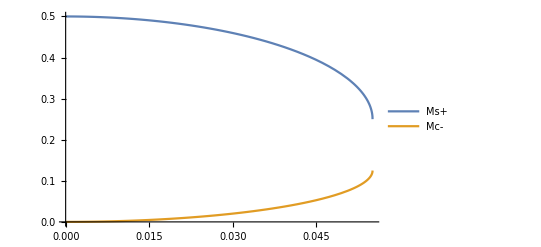

```mathematica
Module[{ℳ=2,κ=0.4},Plot[{(1+√(1-(64 π^2 𝒬^2)/(3 κ^2 ℳ^2)))/4,(1-√(1-(64 π^2 𝒬^2)/(3 κ^2 ℳ^2)))/8},{𝒬,0,Sqrt[3/(64 π^2)κ^2 ℳ^2]},PlotLegends->{"Ms+","Mc-"}]]
```

For Ms+(Mc-) solution, Ms > Mc for any choice of 𝒬, and we have a topological star

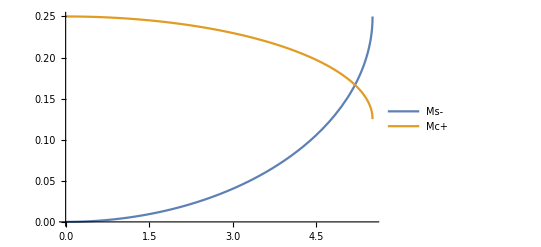

```mathematica
Module[{ℳ=20,κ=4},Plot[{(1-√(1-(64 π^2 𝒬^2)/(3 κ^2 ℳ^2)))/4,(1+√(1-(64 π^2 𝒬^2)/(3 κ^2 ℳ^2)))/8},{𝒬,0,Sqrt[3/(64 π^2)κ^2 ℳ^2]},PlotLegends->{"Ms-","Mc+"}]]
```

For Ms-(Mc+) solution, we can have either Mc > Ms, or Ms > Mc

Is there any condition on 𝒬 or ℳ which changes this behavior?

When does crossing happen?

```mathematica
Solve[(1-√(1-(64 π^2 𝒬^2)/(3 κ^2 ℳ^2)))/4==(1+√(1-(64 π^2 𝒬^2)/(3 κ^2 ℳ^2)))/8,𝒬,PositiveReals]
```

{{𝒬→ConditionalExpression[(√(ℳ^2 κ^2))/(2 √6 π), κ>0&&ℳ>0]}}

For Ms-(Mc+) solution, the critical value of 𝒬 which governs whether we have a topological star or a black string is 𝒬=(ℳ κ)/(2 √6 π). Below this value, Mc > Ms and we have a black string. Above this value, Ms > Mc and we have a topological star.

```mathematica
(*****************************************************************************)
```

```mathematica
-l (1+l) R[r]+((2 Mc Ms^2-Ms (3 Mc+Ms) r+(Mc+Ms) r^2-m^2 Ms r^4+(k^2+m^2) r^5) R[r])/((Ms-r) r^2)+(r^3 ω^2 R[r])/(-Mc+r)+(Mc+Ms-(2 Mc Ms)/r) R'[r]+(Mc-r) (Ms-r) R''[r]
```

Let’s do a general coordinate transformation given by R -> R1/f[r]

```mathematica
Collect[(-l (1+l) R[r]+((2 Mc Ms^2-Ms (3 Mc+Ms) r+(Mc+Ms) r^2-m^2 Ms r^4+(k^2+m^2) r^5) R[r])/((Ms-r) r^2)+(r^3 ω^2 R[r])/(-Mc+r)+(Mc+Ms-(2 Mc Ms)/r) R'[r]+(Mc-r) (Ms-r) R''[r]/.R->Function[r,R1[rs[r]]/f[rs[r]]]//FullSimplify),{R1[rs[r]],R1'[rs[r]],R1''[rs[r]]},FullSimplify]
```

((-Mc+r) (-Ms+r) rs'[r]^2 R1''[rs[r]])/f[rs[r]]+(R1'[rs[r]] ((Mc+Ms-(2 Mc Ms)/r) f[rs[r]] rs'[r]+2 (Mc-r) (-Ms+r) f'[rs[r]] rs'[r]^2+(-Mc+r) (-Ms+r) f[rs[r]] rs''[r]))/f[rs[r]]^2+1/f[rs[r]]^3 R1[rs[r]] (-l (1+l) f[rs[r]]^2+((2 Mc Ms^2-Ms (3 Mc+Ms) r+(Mc+Ms) r^2-m^2 Ms r^4+(k^2+m^2) r^5) f[rs[r]]^2)/((Ms-r) r^2)+(r^3 ω^2 f[rs[r]]^2)/(-Mc+r)+((2 Mc Ms-(Mc+Ms) r) f[rs[r]] f'[rs[r]] rs'[r])/r+(Mc-r) (-Ms+r) rs'[r]^2 (-2 f'[rs[r]]^2+f[rs[r]] f''[rs[r]])+(Mc-r) (-Ms+r) f[rs[r]] f'[rs[r]] rs''[r])

```mathematica
DSolve[(((Mc+Ms-(2 Mc Ms)/r) f[rs[r]] rs'[r]+2 (Mc-r) (-Ms+r) f'[rs[r]] rs'[r]^2+(-Mc+r) (-Ms+r) f[rs[r]] rs''[r])/f[rs[r]]^2==0/.f[rs[r]]->f[r]/.f'[rs[r]]->f'[r]),f[r],r]//FullSimplify
```

{{f[r]→ⅇ^((((2 Mc Ms-(Mc+Ms) K[1]) rs'[K[1]])/((Mc-K[1]) K[1] (-Ms+K[1]))+rs''[K[1]])/(2 rs'[K[1]]^2)K[1]1r) C[1]}}

```mathematica
Collect[1/(r √(-Mc+r) √(-Ms+r))(-l (1+l) R[r]+((2 Mc Ms^2-Ms (3 Mc+Ms) r+(Mc+Ms) r^2-m^2 Ms r^4+(k^2+m^2) r^5) R[r])/((Ms-r) r^2)+(r^3 ω^2 R[r])/(-Mc+r)+(Mc+Ms-(2 Mc Ms)/r) R'[r]+(Mc-r) (Ms-r) R''[r]/.R->Function[r,R1[r]/((√(-Mc+r) √(-Ms+r))/r)]//FullSimplify),{R1[r],R1'[r],R1''[r]},FullSimplify]
```

1/(4 (Mc-r)^2 (Ms-r)^2)(Mc^2+Ms^2-2 Mc Ms (1+2 l (1+l)+2 m^2 r^2)+4 Mc r (l+l^2+(k^2+m^2) r^2)+4 Ms r (l+l^2+r^2 (m-ω) (m+ω))-4 r^2 (l+l^2+r^2 (k^2+m^2-ω^2))) R1[r]+R1''[r]

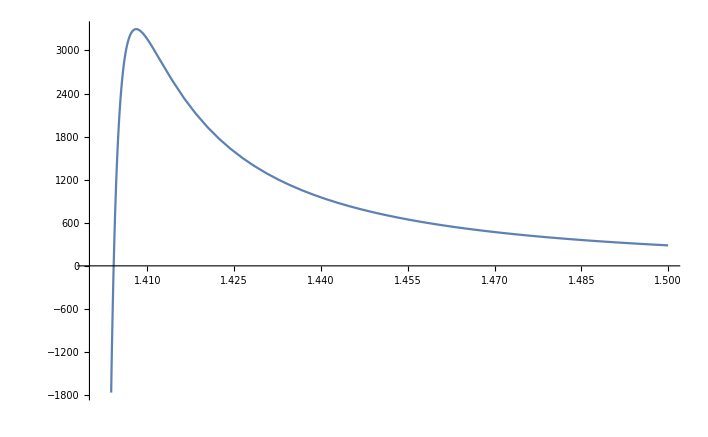

```mathematica
Plot[-1/(4 (Mc-r)^2 (Ms-r)^2)(Mc^2+Ms^2-2 Mc Ms (1+2 l (1+l)+2 m^2 r^2)+4 Mc r (l+l^2+(k^2+m^2) r^2)+4 Ms r (l+l^2+r^2 (m-ω) (m+ω))-4 r^2 (l+l^2+r^2 (k^2+m^2-ω^2)))/.k->0/.m->0/.l->2/.Mc->1.3/.Ms->1.4/.ω->1/10,{r,1.4,1.5}]
```

## Checking Potentials

First equation, which used phi ∝ R1/r

```mathematica
Integrate[r^2/((r-rb)(r-rs)),r]
```

r+(rb^2 Log[r-rb])/(rb-rs)-(rs^2 Log[r-rs])/(rb-rs)

```mathematica
perteqnA=R1''[rs]-(1-rb/r) (1-rs/r) ((l (1+l))/r^2+k^2/(1-rb/r)+(m^2 r^4-2 rb rs+r (rb+rs))/r^4-ω^2/(1-rs/r))R1[rs];
```

```mathematica
perteqnA1=Collect[(r^4/((r-rb)(r-rs))*perteqnA/.R1''[rs]-> (1-rb/r)(1-rs/r)D[(1-rb/r)(1-rs/r)*D[R1[r],r],r]/.R1[rs]->R1[r]),{R1[r],R1'[r],R1''[r]},FullSimplify]
```

(r^4 (-1+rb/r) (1-rs/r) (m^2+(l (1+l))/r^2+(k^2 r)/(r-rb)-(2 rb rs)/r^4+(rb+rs)/r^3-(r ω^2)/(r-rs)) R1[r])/((r-rb) (r-rs))+(rb+rs-(2 rb rs)/r) R1'[r]+(r-rb) (r-rs) R1''[r]

Second equation, which used phi ∝ R2/(r-rs)

```mathematica
Integrate[(r-rs)/(r-rb),r]
```

r+(rb-rs) Log[r-rb]

```mathematica
(r-Ms)/(r-Mc)^3 ((k^2 r^3)/(r-Ms)-(ω^2 r^3)/(r-Mc)+l (1+l)+(Ms-Mc)/(r-Mc)+m^2 r^2)/.Mc->rs/.Ms->rb
```

((r-rb) (l (1+l)+m^2 r^2+(k^2 r^3)/(r-rb)+(rb-rs)/(r-rs)-(r^3 ω^2)/(r-rs)))/(r-rs)^3

```mathematica
perteqnB=R2''[rs]-((r-rb) (l (1+l)+m^2 r^2+(k^2 r^3)/(r-rb)+(rb-rs)/(r-rs)-(r^3 ω^2)/(r-rs)))/(r-rs)^3*R2[rs];
```

```mathematica
perteqnB1=Collect[((r-rs)^3/(r-rb)*perteqnB/.R2''[rs]-> ((r-rb)/(r-rs))D[((r-rb)/(r-rs))*D[R2[r],r],r]/.R2[rs]->R2[r]),{R2[r],R2'[r],R2''[r]},FullSimplify]
```

((-r+rb) (l+l^2+m^2 r^2+(k^2 r^3)/(r-rb)+(rb-rs-r^3 ω^2)/(r-rs)) R2[r])/(r-rb)+(rb-rs) R2'[r]+(r-rb) (r-rs) R2''[r]

```mathematica
(********************************************************************************************)
```

Now, we should be able to swap between the equations by keeping in mind that R1/r=R2/(r-rs)

```mathematica
Collect[r/(r-rs)*perteqnB1/.R2''[r]-> D[(r-rs)/r*R1[r],r,r]/.R2'[r]->D[(r-rs)/r*R1[r],r]/.R2[r]->(r-rs)/r R1[r] ,{R1[r],R1'[r],R1''[r]},FullSimplify]
```

(-l (1+l)+(-m^2 r^4+2 rb rs-r (rb+rs)+r^5 (k^2/(-r+rb)+ω^2/(r-rs)))/r^2) R1[r]+(rb+rs-(2 rb rs)/r) R1'[r]+(r-rb) (r-rs) R1''[r]

does this match original eqn for R1?

```mathematica
(-l (1+l)+(-m^2 r^4+2 rb rs-r (rb+rs)+r^5 (k^2/(-r+rb)+ω^2/(r-rs)))/r^2) R1[r]+(rb+rs-(2 rb rs)/r) R1'[r]+(r-rb) (r-rs) R1''[r]-perteqnA1//FullSimplify
```

0

matches... which is good

```mathematica
Series[(1-rb/r) (1-rs/r) ((l (1+l))/r^2+k^2/(1-rb/r)+(m^2 r^4-2 rb rs+r (rb+rs))/r^4-ω^2/(1-rs/r)),{r,rb,1}]/.k->0/.m->0/.l->2/.rb->31/.rs->29
```

((376-923521 ω^2) (r-31))/28629151+O[r-31]^2

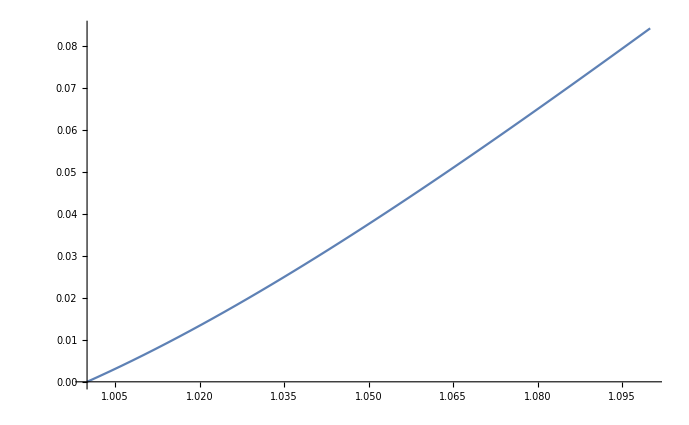

```mathematica
Plot[(1-rb/r) (1-rs/r) ((l (1+l))/r^2+k^2/(1-rb/r)+(m^2 r^4-2 rb rs+r (rb+rs))/r^4-ω^2/(1-rs/r))/.l->2/.rb->1/.rs->0.9/.k->0/.m->0/.ω-> 1/10,{r,1,1.1}]
```

## Leaver with f[r]=r-rs potential

### Finding expansion

Perturbation equation is R’’[rs]-Veff[r]*R[rs]=0. First consider with momentum (k ≠ 0)

```mathematica
Veff=(r-Ms)/(r-Mc)^3 ((k^2 r^3)/(r-Ms)-(ω^2 r^3)/(r-Mc)+l (1+l)+(Ms-Mc)/(r-Mc)-m^2 r^2);
```

at rs --> ∞ (r--> ∞):

```mathematica
Series[Veff,{r,∞,0}]/.m->0//Normal
```

k^2-ω^2

```mathematica
DSolve[R''[rs]+(k^2-ω^2)R[rs]==0,R[rs],rs]/. rs √(-k^2+ω^2)->ⅈ rs √(k^2-ω^2)
```

{{R[rs]→ⅇ^(ⅈ rs √(k^2-ω^2)) C[1]+ⅇ^(-ⅈ rs √(k^2-ω^2)) C[2]}}

Only outgoing modes should be present, so the asymptotic form of the solution should be ∝ ⅇ^(ⅈ rs √(k^2-ω^2))

As rs --> -∞ (r --> Ms):

```mathematica
Series[Veff,{r,Ms,0}]/.m->0//Normal
```

(k^2 Ms^3)/(-Mc+Ms)^3

```mathematica
DSolve[R''[rs]+(k^2 Ms^3)/(-Mc+Ms)^3 R[rs]==0,R[rs],rs]/.(k Ms^(3/2) rs)/(Mc-Ms)^(3/2)-> ⅈ(k Ms^(3/2) rs)/(Ms-Mc)^(3/2)
```

{{R[rs]→ⅇ^((ⅈ k Ms^(3/2) rs)/(-Mc+Ms)^(3/2)) C[1]+ⅇ^(-(ⅈ k Ms^(3/2) rs)/(-Mc+Ms)^(3/2)) C[2]}}

We must have a smooth wave at the boundary r  = Ms, which corresponds to ∂_rs R=0 at rs --> -∞

```mathematica
D[ⅇ^((ⅈ k Ms^(3/2) rs)/(Abs[-Mc+Ms])^(3/2)) C[1]+ⅇ^(-(ⅈ k Ms^(3/2) rs)/(Abs[-Mc+Ms])^(3/2)) C[2],rs]/.rs->r-Ms+(Ms-Mc)Log[r-Ms]/.r->Ms//FullSimplify
```

(ⅈ k Ms^(3/2) (ⅇ^(k (Mc-Ms) (ⅈ ∞) Sign[Ms]^(3/2)) C[1]-ⅇ^(k (-Mc+Ms) (ⅈ ∞) Sign[Ms]^(3/2)) C[2]))/Abs[Mc-Ms]^(3/2)

```mathematica
Solve[(ⅈ k Ms^(3/2) (ⅇ^(k (Mc-Ms) (ⅈ ∞) Sign[Ms]^(3/2)) C[1]-ⅇ^(k (-Mc+Ms) (ⅈ ∞) Sign[Ms]^(3/2)) C[2]))/Abs[Mc-Ms]^(3/2)==0,C[1]]
```

Solve::infc: The system (ⅈ k Ms^(3/2) (ⅇ^(k (Mc+Times[«2»]) (ⅈ ∞) Sign[«1»]^(3/2)) 1-ⅇ^(k (Times[«2»]+Ms) (ⅈ ∞) Sign[«1»]^(3/2)) 2))/Abs[Mc-Ms]^(3/2)==0 contains an infinite object ⅈ ∞.

Solve[(ⅈ k Ms^(3/2) (ⅇ^(k (Mc-Ms) (ⅈ ∞) Sign[Ms]^(3/2)) C[1]-ⅇ^(k (-Mc+Ms) (ⅈ ∞) Sign[Ms]^(3/2)) C[2]))/Abs[Mc-Ms]^(3/2)==0,C[1]]

```mathematica
Solve[(ⅈ k Ms^(3/2) (-Ms+r)^((ⅈ k Ms^(3/2) (-Mc+Ms))/Abs[-Mc+Ms]^(3/2)) C[1])/Abs[-Mc+Ms]^(3/2)-(ⅈ k Ms^(3/2) (-Ms+r)^(-(ⅈ k Ms^(3/2) (-Mc+Ms))/Abs[-Mc+Ms]^(3/2)) C[2])/Abs[-Mc+Ms]^(3/2)]
```

```mathematica
(*****************************************************************************)
```

Perturbation equation is R’’[rs]-Veff[r]*R[rs]=0. no momentum case

```mathematica
Perteqn=R''[rs]-Veff*R[rs]
```

-((-Ms+r) (l (1+l)-m^2 r^2+(-Mc+Ms)/(-Mc+r)+(k^2 r^3)/(-Ms+r)-(r^3 ω^2)/(-Mc+r)) R[rs])/(-Mc+r)^3+R''[rs]

```mathematica
Veff=(r-Ms)/(r-Mc)^3 ((k^2 r^3)/(r-Ms)-(ω^2 r^3)/(r-Mc)+l (1+l)+(Ms-Mc)/(r-Mc)-m^2 r^2);
```

at rs --> ∞ (r--> ∞):

```mathematica
Series[Veff,{r,∞,0}]/.m->0/.k->0//Normal
```

-ω^2

```mathematica
DSolve[R''[rs]+(ω^2)R[rs]==0,R[rs],rs]/.Cos[rs ω]->1/2(Exp[ⅈ rs ω]+Exp[-ⅈ rs ω])/.Sin[rs ω]->1/(2ⅈ)(Exp[ⅈ rs ω]-Exp[-ⅈ rs ω])
```

{{R[rs]→1/2 (ⅇ^(-ⅈ rs ω)+ⅇ^(ⅈ rs ω)) C[1]-1/2 ⅈ (-ⅇ^(-ⅈ rs ω)+ⅇ^(ⅈ rs ω)) C[2]}}

At rs --> -∞ (r-->Ms):

```mathematica
(Series[Veff,{r,Ms,1}]/.m->0/.k->0//Normal)/.r->Ms+Exp[rs/(Ms-Mc)]
```

(ⅇ^(rs/(-Mc+Ms)) (1+l (1+l)-(Ms^3 ω^2)/(-Mc+Ms)))/(-Mc+Ms)^3

define α such that V[r-->Ms]  = α Exp[rs/Ms-Mc]. Then define u such that du/drs = 1/(Ms-Mc), and β = (Ms-Mc)^2 α

```mathematica
DSolve[R''[u]-β Exp[u]R[u]==0,R[u],u]
```

{{R[u]→BesselI[0,2 √(ⅇ^u β)] C[1]+2 BesselK[0,2 √(ⅇ^u β)] C[2]}}

```mathematica
Series[BesselI[0,2 √(ⅇ^u β)],{u,-∞,0}]//Normal//FullSimplify
```

1+ⅇ^u β

Condition we must impose is that the wave must be smooth and derivable at the surface r=Ms.

```mathematica
DSolve[R''[rs]-α Exp[rs/Abs[Ms-Mc]]R[rs]==0,R[rs],rs]
```

{{R[rs]→BesselI[0,2 √(ⅇ^(rs/Abs[-Mc+Ms]) α) Abs[-Mc+Ms]] C[1]+2 BesselK[0,2 √(ⅇ^(rs/Abs[-Mc+Ms]) α) Abs[-Mc+Ms]] C[2]}}

```mathematica
D[BesselI[0,2 √(ⅇ^(rs/Abs[-Mc+Ms]) α) Abs[-Mc+Ms]] C[1]+2 BesselK[0,2 √(ⅇ^(rs/Abs[-Mc+Ms]) α) Abs[-Mc+Ms]] C[2],rs]/.rs->Abs[Ms-Mc]Log[r-Ms]//FullSimplify
```

√((-Ms+r) α) (BesselI[1,2 √((-Ms+r) α) Abs[Mc-Ms]] C[1]-2 BesselK[1,2 √((-Ms+r) α) Abs[Mc-Ms]] C[2])

```mathematica
BesselI[1,2 √((-Ms+r) α) Abs[Mc-Ms]]/.r->Ms
```

0

```mathematica
BesselK[1,2 √((-Ms+r) α) Abs[Mc-Ms]]/.r->Ms
```

ComplexInfinity

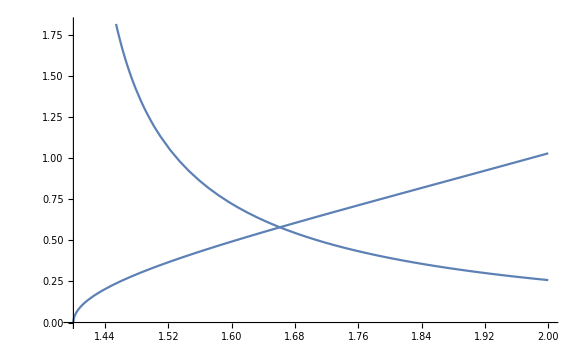

```mathematica
Plot[{BesselK[1,2 √(-Ms+r)],BesselI[1,2 √(-Ms+r)]}/.Ms->1.4,{r,1.4,2}]
```

The BesselK function blows up as r--> Ms, so we must impose its coefficient to be 0:

For rs --> -∞:

```mathematica
R[rs]->BesselI[0,2 √(ⅇ^(rs/Abs[-Mc+Ms]) α) Abs[-Mc+Ms]] C[1]
```

```mathematica
Series[BesselI[0,2 √(ⅇ^(rs/Abs[-Mc+Ms]) α) Abs[-Mc+Ms]] ,{rs,-∞,0}]//Normal//FullSimplify
```

1+ⅇ^(rs/Abs[Mc-Ms]) α Abs[Mc-Ms]^2

```mathematica
Series[(BesselI[0,2 √(ⅇ^(rs/Abs[-Mc+Ms]) α) Abs[-Mc+Ms]/.rs->r-Ms+Abs[Ms-Mc]Log[r-Ms]]) ,{r,Ms,1}]//Normal//FullSimplify
```

1+(-Ms+r) α Abs[Mc-Ms]^2

```mathematica
(D[BesselI[0,2 √(ⅇ^(rs/Abs[-Mc+Ms]) α) Abs[-Mc+Ms]] ,rs])/.rs->r-Ms+Abs[Ms-Mc]Log[r-Ms]/.r->Ms//Simplify
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 α ComplexInfinity encountered.

Indeterminate

```mathematica
(*************************************************************************************)
```

```mathematica
(*************************************************************************************)
```

```mathematica
(*************************************************************************************)
```

```mathematica
Veff=(r-Ms)/(r-Mc)^3 ((k^2 r^3)/(r-Ms)-(ω^2 r^3)/(r-Mc)+l (1+l)+(Ms-Mc)/(r-Mc)-m^2 r^2)/.Mc->rs/.Ms->rb;
```

```mathematica
(Veff//Distribute//FullSimplify)/.r->rs
```

Power::infy: Infinite expression 1/0^4 encountered.

ComplexInfinity

```mathematica
Perteqn=R''[rs]-Veff*R[rs]
```

-((r-rb) (l (1+l)-m^2 r^2+(k^2 r^3)/(r-rb)+(rb-rs)/(r-rs)-(r^3 ω^2)/(r-rs)) R[rs])/(r-rs)^3+R''[rs]

For the expansion, the method of Frobenius is useful:

```mathematica
Solve[f==((r-rb)/(r-rs)),r]//FullSimplify
```

{{r→(-rb+f rs)/(-1+f)}}

```mathematica
Perteqn1=Perteqn/.R''[rs]->((r-rb)/(r-rs))*(((r-rb)/(r-rs))*R''[r]+R'[r]*D[((r-rb)/(r-rs)),r])/.R[rs]->R[r]/.Ms->rb/.Mc->rs//FullSimplify
```

((r-rb) (-(l+l^2-m^2 r^2+(k^2 r^3)/(r-rb)+(rb-rs-r^3 ω^2)/(r-rs)) R[r]+(rb-rs) R'[r]+(r-rb) (r-rs) R''[r]))/(r-rs)^3

```mathematica
Perteqn2=Perteqn1/.R[r]->R[f]/.R'[r]->D[((r-rb)/(r-rs)),r]*R'[f]/.R''[r]->R'[f]*D[((r-rb)/(r-rs)),r,r]+(D[((r-rb)/(r-rs)),r])^2*R''[f]/.r->(-rb+f rs)/(-1+f)//FullSimplify
```

1/(rb-rs)^3((-k^2 rb^3+f (-(1+l+l^2) rb+rs+l (1+l) rs+(3 k^2-m^2) rb^2 rs+rb^3 (m^2+ω^2))-f^2 ((3+2 l (1+l)) rs-rb (3+2 l (1+l)+(-3 k^2+2 m^2) rs^2)+rb^2 rs (2 m^2+3 ω^2))+f^4 (rb-rs (1+rs^2 ω^2))+f^3 (rs (3+l+l^2+(k-m) (k+m) rs^2)-rb (3+l+l^2-rs^2 (m^2+3 ω^2)))) R[f]+(-1+f)^3 f (rb-rs) ((-1+3 f) R'[f]+(-1+f) f R''[f]))

```mathematica
PertEqn3=Collect[(rb-rs)^2/(-1+f)^4 Perteqn2,{R''[f],R'[f],R[f]},FullSimplify]
```

1/((-1+f)^4 (rb-rs))(-k^2 rb^3+f (-(1+l+l^2) rb+rs+l (1+l) rs+(3 k^2-m^2) rb^2 rs+rb^3 (m^2+ω^2))-f^2 ((3+2 l (1+l)) rs-rb (3+2 l (1+l)+(-3 k^2+2 m^2) rs^2)+rb^2 rs (2 m^2+3 ω^2))+f^4 (rb-rs (1+rs^2 ω^2))+f^3 (rs (3+l+l^2+(k-m) (k+m) rs^2)-rb (3+l+l^2-rs^2 (m^2+3 ω^2)))) R[f]+(3+2/(-1+f)) f R'[f]+f^2 R''[f]

```mathematica
PertEqn3/.f->0
```

-(k^2 rb^3 R[0])/(rb-rs)

```mathematica
q[x_]:=Coefficient[PertEqn3,R[f]]/.f->x
```

```mathematica
p[x_]:=1/f*Coefficient[PertEqn3,R'[f]]/.f->x
```

```mathematica
q0=Limit[q[x],x->0]
```

-(k^2 rb^3)/(rb-rs)

```mathematica
p0=Limit[p[x],x->0]
```

1

```mathematica
Solve[x(x-1)+p0*x+q0==0,x]
```

{{x→-(k rb^(3/2))/(√(rb-rs))},{x→(k rb^(3/2))/(√(rb-rs))}}

Expansion becomes :

```mathematica
u[r]=((r-rp)/r)^(-(rp^2 ρ)/(rm-rp))Sum[Subscript[b, n]*((r-rp)/r)^n,{n,0,∞}]
```

((r-rp)/r)^(-(rp^2 ρ)/(rm-rp)) ∑_(n=0)^∞ ((r-rp)/r)^n b_n

```mathematica
(D[f[r]*Exp[ⅈ ω (r-rs)]Sum[Subscript[a, n]((r-rs)/(r-rb))^n,{n,0,∞}],r]//FullSimplify)
```

ⅇ^(ⅈ (r-rs) ω) (f[r] (ⅈ ω ∑_(n=0)^∞ ((r-rs)/(r-rb))^n a_n+∑_(n=0)^∞ (-(n r ((r-rs)/(r-rb))^(-1+n))/(r-rb)^2+(n ((r-rs)/(r-rb))^(-1+n))/(r-rb)+(n ((r-rs)/(r-rb))^(-1+n) rs)/(r-rb)^2) a_n)+(∑_(n=0)^∞ ((r-rs)/(r-rb))^n a_n) f'[r])

```mathematica
D[(r-rb)/(r-rs),r]//FullSimplify
```

(rb-rs)/(r-rs)^2

```mathematica
((r-rb)/r)^2 r^(ⅈ ω(rb-rs))ⅇ^(ⅈ ω(r-rb))Sum[Subscript[a, n]((r-rb)/(r-rs))^n,{n,0,∞}]
```

ⅇ^(ⅈ (r-rb) ω) r^(-2+ⅈ (rb-rs) ω) (r-rb)^2 ∑_(n=0)^∞ ((r-rb)/(r-rs))^n a_n

```mathematica
D[((r-rb)/r)^2 r^(ⅈ ω(rb-rs))ⅇ^(ⅈ ω(r-rb))(Sum[Subscript[a, n]((r-rb)/(r-rs))^n,{n,0,∞}]),r]//FullSimplify
```

ⅇ^(ⅈ (r-rb) ω) r^(-3+ⅈ (rb-rs) ω) (r-rb) (r (r-rb) ∑_(n=0)^∞ (-(n r ((r-rb)/(r-rs))^(-1+n))/(r-rs)^2+(n rb ((r-rb)/(r-rs))^(-1+n))/(r-rs)^2+(n ((r-rb)/(r-rs))^(-1+n))/(r-rs)) a_n+(2 rb+ⅈ (r-rb) (r+rb-rs) ω) ∑_(n=0)^∞ ((r-rb)/(r-rs))^n a_n)

```mathematica
%/.r->rb
```

Power::indet: Indeterminate expression 0^0 encountered.

0

ⅇ^(ⅈ r ω-ⅈ rb ω) r^(ⅈ (rb-rs) ω) (1-(2 rb)/r+rb^2/r^2) ∑_(n=0)^∞ (a_n+(n (-rb+rs) a_n)/r)

### Using expansion to find recurrence relations

```mathematica
Perteqn=((-r+rb) (l+l^2+m^2 r^2+(k^2 r^3)/(r-rb)+(rb-rs-r^3 ω^2)/(r-rs)) R2[r])/(r-rb)+(rb-rs) R2'[r]+(r-rb) (r-rs) R2''[r]
```

((-r+rb) (l+l^2+m^2 r^2+(k^2 r^3)/(r-rb)+(rb-rs-r^3 ω^2)/(r-rs)) R2[r])/(r-rb)+(rb-rs) R2'[r]+(r-rb) (r-rs) R2''[r]

```mathematica
Series[R2''[rs]-((r-rb) (l (1+l)+m^2 r^2+(k^2 r^3)/(r-rb)+(rb-rs)/(r-rs)-(r^3 ω^2)/(r-rs)))/(r-rs)^3*R2[rs],{r,∞,0}]/.k->0/.m->0//Normal//FullSimplify
```

ω^2 R2[rs]+R2''[rs]

```mathematica
Series[1/r^2*Perteqn,{r,∞,0}]/.k->0/.m->0//Normal//FullSimplify
```

ω^2 R2[r]+R2''[r]

Use the following expansion:

```mathematica
ϕ[r]=ⅇ^(ⅈ (r-rb) ω) r^(-2+ⅈ (rb-rs) ω) (r-rb)^2 ∑_(n=0)^∞ ((r-rb)/(r-rs))^n Subscript[a, n]
```

```mathematica
A[r_]:=ⅇ^(-ⅈ r ω) /.ω->ⅈ ρ
```

Restrict to n^thentry in the master eqn.

```mathematica
fr[r_]:=(r-rb)/(r-rs);
```

```mathematica
rredef=Solve[f==fr[r],r][[1,1,2]]//FullSimplify
```

(-rb+f rs)/(-1+f)

```mathematica
Zn=AA[r] Subscript[b, n] fr[r]^n//FullSimplify;
dZn=D[Zn,r]/.r->rredef//FullSimplify;
ddZn=D[D[Zn,r],r]/.r->rredef//FullSimplify;
dAoverA=D[A[r],r]/A[r]/.r->rredef//FullSimplify;
ddAoverA=D[D[A[r],r],r]/A[r]/.r->rredef//FullSimplify;
```

Rewrite the radial eqn:

```mathematica
Perteqn/.k->0/.m->0/.ω->ⅈ ρ
```

((-r+rb) (l+l^2+(rb-rs+r^3 ρ^2)/(r-rs)) R2[r])/(r-rb)+(rb-rs) R2'[r]+(r-rb) (r-rs) R2''[r]

```mathematica
firstterm=(r-rb) (r-rs) ddZn/AA[r]/.r->rredef/.AA'[rredef]->dAoverA*AA[rredef]/.AA''[rredef]-> ddAoverA*AA[rredef]//Expand//FullSimplify
```

(f^(-1+n) ((-1+f)^4 n^2+f^2 (rb-rs)^2 ρ^2+(-1+f)^2 n (-1+f^2+2 f (rb-rs) ρ)) b_n)/(-1+f)^2

```mathematica
secondterm=(rb-rs) dZn/AA[r]/.r->rredef/.AA'[rredef]->dAoverA*AA[rredef]/.AA''[rredef]-> ddAoverA*AA[rredef]//Expand//FullSimplify
```

f^(-1+n) ((-1+f)^2 n+f (rb-rs) ρ) b_n

```mathematica
thirdterm=((-r+rb) (l+l^2+(rb-rs+r^3 ρ^2)/(r-rs)))/(r-rb)*Zn/AA[r]/.r->rredef//Expand//FullSimplify
```

f^n (-1+f-l (1+l)+((-rb+f rs)^3 ρ^2)/((-1+f)^2 (rb-rs))) b_n

```mathematica
mastereqn=(firstterm+secondterm+thirdterm)//Expand//FullSimplify
```

f^n ((n^2+f^2 (1+n)^2-f (1+l+l^2+2 n (1+n)))/f+(1+2 n) (rb-rs) ρ+((rb^3-3 f rb rs^2+f (1+f) rs^3) ρ^2)/((-1+f) (rb-rs))) b_n

```mathematica
mastereqn1=Collect[((1/(f^(n-1)/((-1+f)(rb-rs)))*mastereqn//Expand//FullSimplify)),{f,f^2,f^3,f^4,f^5},FullSimplify]
```

n^2 (-rb+rs) b_n+f ((1+l+l^2+n (2+3 n)) (rb-rs)-(1+2 n) (rb-rs)^2 ρ+rb^3 ρ^2) b_n+f^3 ((1+n)^2 (rb-rs)+rs^3 ρ^2) b_n+f^2 (-(2+l+l^2+n (4+3 n)) (rb-rs)+(1+2 n) (rb-rs)^2 ρ+rs^2 (-3 rb+rs) ρ^2) b_n

```mathematica
Coefficient[mastereqn1,f,0]/.n->n+1//FullSimplify
```

(1+n)^2 (-rb+rs) b_(1+n)

```mathematica
Coefficient[mastereqn1,f,1]/.n->n//FullSimplify
```

((1+l+l^2+n (2+3 n)) (rb-rs)-(1+2 n) (rb-rs)^2 ρ+rb^3 ρ^2) b_n

```mathematica
Coefficient[mastereqn1,f,2]/.n->n-1//FullSimplify
```

(-(1+l+l^2+n (-2+3 n)) (rb-rs)+(-1+2 n) (rb-rs)^2 ρ+rs^2 (-3 rb+rs) ρ^2) b_(-1+n)

```mathematica
Coefficient[mastereqn1,f,3]/.n->n-2//FullSimplify
```

((-1+n)^2 (rb-rs)+rs^3 ρ^2) b_(-2+n)

```mathematica
Coefficient[mastereqn1,f,4]/.n->n-3//FullSimplify
```

0

## Leaver with f[r] = r potential

```mathematica
Integrate[r^2/((r-rb)(r-rs)),r]
```

r+(rb^2 Log[r-rb])/(rb-rs)-(rs^2 Log[r-rs])/(rb-rs)

```mathematica
perteqnA=R1''[rs]-(1-rb/r) (1-rs/r) ((l (1+l))/r^2+k^2/(1-rb/r)+(m^2 r^4-2 rb rs+r (rb+rs))/r^4-ω^2/(1-rs/r))R1[rs];
```

```mathematica
perteqnA1=Collect[(r^4/((r-rb)(r-rs))*perteqnA/.R1''[rs]-> (1-rb/r)(1-rs/r)D[(1-rb/r)(1-rs/r)*D[R1[r],r],r]/.R1[rs]->R1[r]),{R1[r],R1'[r],R1''[r]},FullSimplify]
```

(r^4 (-1+rb/r) (1-rs/r) (m^2+(l (1+l))/r^2+(k^2 r)/(r-rb)-(2 rb rs)/r^4+(rb+rs)/r^3-(r ω^2)/(r-rs)) R1[r])/((r-rb) (r-rs))+(rb+rs-(2 rb rs)/r) R1'[r]+(r-rb) (r-rs) R1''[r]

```mathematica
perteqnA1/.rb->0/.rs->1/.k->0/.m->0/.ω->ⅈ ρ//FullSimplify
```

(-l (1+l)-1/r-(r^3 ρ^2)/(-1+r)) R1[r]+R1'[r]+(-1+r) r R1''[r]

### Deriving Recurrence Relation

```mathematica
PertEqn=(r^4 (-1+rb/r) (1-rs/r) (m^2+(l (1+l))/r^2+(k^2 r)/(r-rb)-(2 rb rs)/r^4+(rb+rs)/r^3-(r ω^2)/(r-rs)) R1[r])/((r-rb) (r-rs))+(rb+rs-(2 rb rs)/r) R1'[r]+(r-rb) (r-rs) R1''[r];
```

```mathematica
Integrate[(1-rb/r)^-1(1-rs/r)^-1,r]
```

r+(rb^2 Log[r-rb])/(rb-rs)-(rs^2 Log[r-rs])/(rb-rs)

```mathematica
Series[r+(rb^2 Log[r-rb])/(rb-rs)-(rs^2 Log[r-rs])/(rb-rs),{r,∞,0}]//Normal//FullSimplify
```

r+(rb+rs) Log[r]

Use the following expansion:

```mathematica
ⅇ^(ⅈ (r-rb) ω) r^(-2+ⅈ (rb+rs) ω) (r-rb)^2 ∑_(n=0)^∞ ((r-rb)/(r-rs))^n Subscript[a, n]
```

```mathematica
(D[A[r],r]*Subscript[a, 0]+A[r]*Subscript[a, 1]/(rb-rs)//FullSimplify)/.r->rb//FullSimplify
```

ⅇ^(-rb ρ) rb^(-(rb^2 ρ)/(rb-rs)) (rb-rs)^(-2+(rs^2 ρ)/(rb-rs)) (rb (-2 rb+3 rs) ρ a_0+(rb-rs) a_1)

```mathematica
(Series[A[r],{r,rb,0}]//Normal//FullSimplify)
```

ⅇ^(-rb ρ) rb^(-(rb^2 ρ)/(rb-rs)) (rb-rs)^((rs^2 ρ)/(rb-rs))

```mathematica
A[r_]:=ⅇ^(ⅈ r ω) (r)^(ⅈ ω rb^2/(rb-rs))(r-rs)^(-ⅈ ω rs^2/(rb-rs))/.ω->ⅈ ρ
```

```mathematica
A[r_]:=ⅇ^(ⅈ( r-rs) ω)r/(r-rs) (*(r)^(ⅈ ω (rb+rs))((r-rs)/r)^(-ⅈ ω rs^2/(rs-rb))*)/.ω->ⅈ ρ
```

```mathematica
A[r]/.rs->1/.rb->0
```

ⅇ^(-r ρ) (-1+r)^-ρ

Restrict to n^thentry in the master eqn.

```mathematica
fr[r_]:=(r-rb)/(r-rs);
```

```mathematica
rredef=Solve[f==fr[r],r][[1,1,2]]//FullSimplify
```

(-rb+f rs)/(-1+f)

```mathematica
Zn=AA[r] Subscript[b, n] fr[r]^n//FullSimplify;
dZn=D[Zn,r]/.r->rredef//FullSimplify;
ddZn=D[D[Zn,r],r]/.r->rredef//FullSimplify;
dAoverA=D[A[r],r]/A[r]/.r->rredef//FullSimplify;
ddAoverA=D[D[A[r],r],r]/A[r]/.r->rredef//FullSimplify;
```

Rewrite the radial eqn:

```mathematica
PertEqn/.k->0/.m->0
```

-l (1+l) R[r]+((2 rb^2 rs+r^2 (rb+rs)-r rb (rb+3 rs)) R[r])/(r^2 (-r+rb))+(r^3 ω^2 R[r])/(r-rs)+(rb+rs-(2 rb rs)/r) R'[r]+(-r+rb) (-r+rs) R''[r]

```mathematica
firstterm=(r-rb) (r-rs) ddZn/AA[r]/.r->rredef/.AA'[rredef]->dAoverA*AA[rredef]/.AA''[rredef]-> ddAoverA*AA[rredef]//Expand//FullSimplify
```

1/((-1+f)^2 (-rb+f rs))f^(-1+n) ((-1+f)^3 (-n (1+f+(-1+f) n) rb+f (1+n) (-n+f (2+n)) rs)-2 (-1+f)^2 f (rb-rs) (-n rb+f (1+n) rs) ρ+f^2 (rb-rs)^2 (-rb+f rs) ρ^2) b_n

```mathematica
secondterm=(rb+rs-(2 rb rs)/r)  dZn/AA[r]/.r->rredef/.AA'[rredef]->dAoverA*AA[rredef]/.AA''[rredef]-> ddAoverA*AA[rredef]//Expand//FullSimplify
```

-(f^(-1+n) (rb+f rs) ((-1+f)^2 (-n rb+f (1+n) rs)+f (rb-rs) (rb-f rs) ρ) b_n)/(rb-f rs)^2

```mathematica
thirdterm=(-l (1+l)+(2 rb^2 rs+r^2 (rb+rs)-r rb (rb+3 rs))/(r^2 (-r+rb))-(r^3 ρ^2)/(r-rs))*Zn/AA[r]/.r->rredef//Expand//FullSimplify
```

(f^n (-(1-f+l+l^2) rb^2+(1+f^2+2 f (-1+l+l^2)) rb rs-f (-1+f (1+l+l^2)) rs^2+((-rb+f rs)^5 ρ^2)/((-1+f)^2 (rb-rs))) b_n)/(rb-f rs)^2

```mathematica
mastereqn=(firstterm+secondterm+thirdterm)//Expand//FullSimplify
```

f^n ((n^2+f^2 (1+n)^2-f (1+l+l^2+2 n (1+n)))/f-(1+2 n) (rb-rs) ρ+((rb^3-3 f rb rs^2+f (1+f) rs^3) ρ^2)/((-1+f) (rb-rs))) b_n

```mathematica
mastereqn1=(mastereqn*1/(f^(-1+n)/((-1+f) (rb-rs)))//Expand)//FullSimplify
```

((-1+f) (n^2+f^2 (1+n)^2-f (1+l+l^2+2 n (1+n))) (rb-rs)-(-1+f) f (1+2 n) (rb-rs)^2 ρ+f (rb^3-3 f rb rs^2+f (1+f) rs^3) ρ^2) b_n

```mathematica
Coefficient[mastereqn1,f,0]/.n->n+1//FullSimplify
```

(1+n)^2 (-rb+rs) b_(1+n)

```mathematica
Coefficient[mastereqn1,f,1]/.n->n//FullSimplify
```

((1+l+l^2+n (2+3 n)) (rb-rs)+(1+2 n) (rb-rs)^2 ρ+rb^3 ρ^2) b_n

```mathematica
Coefficient[mastereqn1,f,2]/.n->n-1//FullSimplify
```

-((1+l+l^2+n (-2+3 n)) (rb-rs)+(-1+2 n) (rb-rs)^2 ρ+(3 rb-rs) rs^2 ρ^2) b_(-1+n)

```mathematica
Coefficient[mastereqn1,f,3]/.n->n-2//FullSimplify
```

((-1+n)^2 (rb-rs)+rs^3 ρ^2) b_(-2+n)

```mathematica
Coefficient[mastereqn1,f,4]/.n->n-3//FullSimplify
```

0

```mathematica
Coefficient[mastereqn1,f,5]/.n->n-4//FullSimplify
```

0

## Using Recurrence Relation to Compute QNM’s

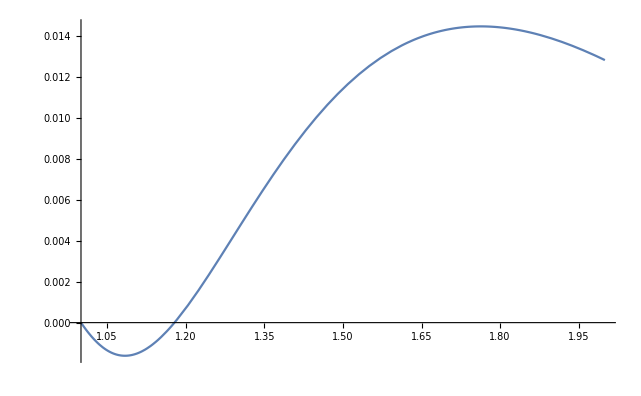

```mathematica
Plot[(1-rb/r) (1-rs/r) ((l (1+l))/r^2+k^2/(1-rb/r)+(m^2 r^4-2 rb rs+r (rb+rs))/r^4-ω^2/(1-rs/r))/.l->0/.rb->1/.rs->0.95/.k->0/.m->0/.ω->1/5,{r,1,2}]
```

Need to do Gaussian elimination to get a three term recurrence relation

```mathematica
αn=Function[n,(1+n)^2 (-rb+rs) ];
βn=Function[n,((1+l+l^2+n (2+3 n)) (rb-rs)-(1+2 n) (rb-rs)^2 ρ+rb^3 ρ^2)];
γn=Function[n,(-(1+l+l^2+n (-2+3 n)) (rb-rs)+(-1+2 n) (rb-rs)^2 ρ+rs^2 (-3 rb+rs) ρ^2) ];
δn=Function[n,((-1+n)^2 (rb-rs)+rs^3 ρ^2)];
```

For 4 term relations:

```mathematica
FourTermCoeffs[n_]:=Join[{Join[{βn[0],αn[0]},Array[0*#&,n]]},{Join[{γn[1],βn[1],αn[1]},Array[0*#&,(n)-1]]},Table[Join[Array[0*#&,i-2],{δn[i],γn[i],βn[i],αn[i]},Array[0*#&,(n)-i]],{i,2,n}]]/.l->0/.rb->1/.rs->0.95
```

```mathematica
GaussReducedCoeffs[n_]:=Module[{newrow,initialcoeffs=FourTermCoeffs[n],newcoeffs},
newcoeffs=For[i=3,i≤ Length[initialcoeffs],i++,newrow=Simplify[initialcoeffs[[i]]-initialcoeffs[[i,i-2]]/initialcoeffs[[i-1,i-2]]*initialcoeffs[[i-1]]]; initialcoeffs[[i]]=newrow];
initialcoeffs]
```

```mathematica
coeffs=GaussReducedCoeffs[200];
```

```mathematica
Leaver[Nmax_]:=Module[{rplus,rminus,αprime,βprime,γprime,RN,iMAX=Nmax,coeffs1},
αprime[n_]:=coeffs[[n+1,n+2]];
βprime[n_]:=coeffs[[n+1,n+1]];
γprime[n_]:=coeffs[[n+1,n]];
For[{i=iMAX;RN=-1.0;},i>0,i--,RN=(-γprime[i])/(βprime[i]+αprime[i]RN)];(βprime[0]/αprime[0]+RN)]
```

```mathematica
FindRoot[Leaver[100]==0,{ρ,-0.02154055819138901+1.7226996636523288 ⅈ,0.028316595057755464-0.9866515780063476 ⅈ}]
Leaver[100]/.%
```

{ρ→0.0122148-0.977935 ⅈ}

1.13811×10^-11-1.27464×10^-11 ⅈ

```mathematica
NSolve[Leaver[4]==0,ρ]
```

{{ρ→0.00528328-0.945522 ⅈ},{ρ→0.00528328+0.945522 ⅈ},{ρ→0.00833125-0.677909 ⅈ},{ρ→0.00833125+0.677909 ⅈ},{ρ→0.0072917-0.42673 ⅈ},{ρ→0.0072917+0.42673 ⅈ},{ρ→0.00206051-0.213264 ⅈ},{ρ→0.00206051+0.213264 ⅈ}}

```mathematica
Plot3D[Abs[Leaver[40]]/.{ρ->x+I y},{x,-1/10,1/10},{y,-1,1},PlotRange->{Automatic,Automatic,{0,1/10}}]
```

-Graphics3D-

For l=0:

```mathematica
FindRoot[Leaver[1]==0,{ρ,0.012384367619098124-0.9089482860581204 ⅈ}]
Leaver[10]/.%
```

{ρ→0.00140503-0.221254 ⅈ}

0.0278887-0.00188746 ⅈ

```mathematica
(*this is fine*)
```

```mathematica
Module[{Nmax=10,guess},
guess=FindRoot[Leaver[1]==0,{ρ,0.0014050320626488068-0.22125366329427723 ⅈ}];For[i=1,i<Nmax,i++,neww=FindRoot[Leaver[i]==0,{ρ,guess}][[1,2]];
guess=neww;];guess]
```

FindRoot::srect: Value {ρ→0.00140503-0.221254 ⅈ} in search specification {ρ,guess$251781} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {AccuracyGoal→Automatic,Compiled→Automatic,DampingFactor→1,Evaluated→True,EvaluationMonitor→None,Jacobian→Automatic,MaxIterations→100,Method→Automatic,PrecisionGoal→Automatic,StepMonitor→None,WorkingPrecision→MachinePrecision}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[FindRoot::optrs,Hold[{AccuracyGoal→Automatic,Compiled→Automatic,DampingFactor→1,Evaluated→True,EvaluationMonitor→None,Jacobian→Automatic,MaxIterations→100,Method→Automatic,PrecisionGoal→Automatic,StepMonitor→None,WorkingPrecision→MachinePrecision}],Options[FindRoot]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {AccuracyGoal→Automatic,Compiled→Automatic,DampingFactor→1,Evaluated→True,EvaluationMonitor→None,Jacobian→Automatic,MaxIterations→100,Method→Automatic,PrecisionGoal→Automatic,StepMonitor→None,WorkingPrecision→MachinePrecision}.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{FindRoot::srect,FindRoot::srect,FindRoot::srect,General::stop,$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

FindRoot::srect: Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect,$IterationLimit::itlim}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

FindRoot::srect: Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect,$IterationLimit::itlim,FindRoot::srect,General::stop,$IterationLimit::itlim}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

FindRoot::srect: Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect,$IterationLimit::itlim}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$Aborted[]

FindRoot::srect: Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect,FindRoot::srect,General::stop,$IterationLimit::itlim}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

FindRoot::srect: Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect,$IterationLimit::itlim}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

FindRoot::srect: Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect,$IterationLimit::itlim,FindRoot::srect,General::stop,$IterationLimit::itlim}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

FindRoot::srect: Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect,$IterationLimit::itlim}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

FindRoot::srect: Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect,$IterationLimit::itlim,FindRoot::srect,General::stop,$IterationLimit::itlim}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

FindRoot::srect: Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect,$IterationLimit::itlim}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

FindRoot::srect: Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect,$IterationLimit::itlim,FindRoot::srect,General::stop,$IterationLimit::itlim}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$Aborted[]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$Aborted[]

FindRoot::srect: Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.

$Aborted[]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect,FindRoot::srect,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$Aborted[]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$Aborted

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$Aborted[]

FindRoot::srect: Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.

$Aborted[]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect,FindRoot::srect,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$Aborted[]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$Aborted[]

FindRoot::srect: Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.

$Aborted[]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect,FindRoot::srect,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$Aborted[]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$Aborted[]

FindRoot::srect: Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.

$Aborted[]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect,FindRoot::srect,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$Aborted[]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$Aborted[]

FindRoot::srect: Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.

$Aborted[]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect,FindRoot::srect,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$Aborted[]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$Aborted[]

FindRoot::srect: Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.

$Aborted[]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect,FindRoot::srect,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$Aborted[]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

FindRoot::srect: Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect,FindRoot::srect,$IterationLimit::itlim,FindRoot::srect,General::stop,$IterationLimit::itlim}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,FindRoot::srect}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[FindRoot::srect :  Value FindRoot[Leaver[i]==0.,{ρ,guess$251781}] in search specification {ρ,guess$251781} is not a number or array of numbers.]

```mathematica
For[i=1,i<Nmax,i++,neww=FindRoot[Leaver[i]==0,{ρ,guess}];
guess=neww; guess]
```